## Numerical calculations for orbits

We first have to initialise xAct, and set it up to use the Schwarzschild chart. We also constrain variables to remain in the region under the event horizon.

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->16,FontColor->Black};
```

```mathematica
<<xAct`xCoba`
<<xAct`ShowTime1`;
$RecursionLimit=Infinity;
Off[General::spell];
$DefInfoQ=False;
$CVVerbose=False;
$xCobaCacheVerbose=False;
$PrePrint=ScreenDollarIndices;
$Post=ScreenDollarIndices;
$CVSimplify=Together;
$CVReplace=False;
$CovDFormat="Postfix";
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M4,4,{μ,ν,α,β,σ}]
```

```mathematica
DefConstantSymbol[M]
```

```mathematica
DefChart[schw,M4, Range[0,3], {t[],r[],θ[],ϕ[]},FormatBasis->{"Partials","Differentials"},ChartColor->Red]
```

```mathematica
$Assumptions=And[
(t[]|r[]|θ[]|ϕ[])∈Reals,
2M>r[]>0,
0<=ϕ[],
M>0
];
```

```mathematica
gschw = CTensor[DiagonalMatrix[{-(1-(2M)/r[]),(1-(2M)/r[])^-1,r[]^2,(r[] Sin[θ[]])^2}],{-schw,-schw},0]
```

CTensor[{{-1+(2 M)/r,0,0,0},{0,1/(1-(2 M)/r),0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-schw,-schw},0]

```mathematica
SetCMetric[gschw,schw,SignatureOfMetric->{3,1,0}]
```

Having set up the chart, we go straight to computing the necessary geometric tensors needed for calculations (Riemann tensor, Ricci tensor, and the Christoffel symbols for the covariant derivative).

```mathematica
CDschw=CovDOfMetric[gschw]//FullSimplify;
```

```mathematica
MetricCompute[gschw,schw,All]//AbsoluteTiming
```

{0.051111,Null}

```mathematica
Christoffel[CDschw,PDschw][α,-β,-δ]//FullSimplify
```

0
M/(r (-2 M+r))
0
0 | M/(r (-2 M+r))
0
0
0 | 0
0
0
0 | 0
0
0
0
(M (-2 M+r))/r^3
0
0
0 | 0
M/(2 M r-r^2)
0
0 | 0
0
2 M-r
0 | 0
0
0
(2 M-r) Sin[θ]^2
0
0
0
0 | 0
0
1/r
0 | 0
1/r
0
0 | 0
0
0
-Cos[θ] Sin[θ]
0
0
0
0 | 0
0
0
1/r | 0
0
0
Cot[θ] | 0
1/r
Cot[θ]
0 | α |   |  
  | β | δ

```mathematica
Riemann[CDschw][-α,-β,-δ,σ]//FullSimplify
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (2 M (2 M-r))/r^4 | 0 | 0
-(2 M)/(r^2 (-2 M+r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4 | 0
0 | 0 | 0 | 0
M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (M (-2 M+r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(M Sin[θ]^2)/r | 0 | 0 | 0
0 | (2 M (-2 M+r))/r^4 | 0 | 0
(2 M)/(r^2 (-2 M+r)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/((2 M-r) r^2) | 0
0 | M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/((2 M-r) r^2)
0 | 0 | 0 | 0
0 | (M Sin[θ]^2)/r | 0 | 0
0 | 0 | (M (2 M-r))/r^4 | 0
0 | 0 | 0 | 0
-M/r | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | M/(r^2 (-2 M+r)) | 0
0 | -M/r | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (2 M)/r
0 | 0 | -(2 M Sin[θ]^2)/r | 0
0 | 0 | 0 | (M (2 M-r))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | M/(r^2 (-2 M+r))
0 | 0 | 0 | 0
0 | -(M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(2 M)/r
0 | 0 | (2 M Sin[θ]^2)/r | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 |   |   |   | σ
α | β | δ |

```mathematica
Ricci[CDschw][-α,-β]//FullSimplify
```

0

## Numerical calculations of geodesic equation

Now that we’re done with the charts, it’s time to create some curves. We’ll start with geodesics, and focus on purely radial infall first. The motion is restricted to the plane.

```mathematica
$Assumptions=And[$Assumptions,θ[]==π/2]
```

(t|r|θ|ϕ)∈ℝ&&2 M>r>0&&0≤ϕ&&M>0&&θ==π/2

```mathematica
DefParameter[λ]
DefParameter[τ]
DefConstantSymbol[amag]
DefScalarFunction/@{γt,γr,γϕ,at,ar,aϕ,e,L};
```

```mathematica
x={γt[λ],γr[λ],π/2,γϕ[λ]}
u=CTensor[D[x,λ],{schw},0]
a = CTensor[ {at[λ],ar[λ],0,aϕ[λ]},{schw},0]
```

{γt[λ],γr[λ],π/2,γϕ[λ]}

CTensor[{γt'[λ],γr'[λ],0,γϕ'[λ]},{schw},0]

CTensor[{at[λ],ar[λ],0,aϕ[λ]},{schw},0]

We can also define our functions representing individual constants.

```mathematica
constants=Flatten@{Solve[u[-ν]  CTensor[{0,0,0,1},{schw},0][ν]==L[λ],γϕ'[λ]],Solve[u[-ν] CTensor[{1,0,0,0},{schw},0][ν]==e[λ]//FullSimplify,γt'[λ]]}
```

{γϕ'[λ]→L[λ]/r^2,γt'[λ]→-(e[λ] r)/(-2 M+r)}

```mathematica
u[μ]/.constants//FullSimplify
```

(e[λ] r)/(2 M-r)
γr'[λ]
0
L[λ]/r^2 | μ

In any general relativity calculation, we want to use certain constants of motion. In this case, since our constants e and L will be subject to change due to thrust applied by rocket engines, we cannot take them as constant. However, we still have the normalisation of the 4-velocity; the normalisation of the 4-acceleration; and the orthogonality of the 4-velocity to 4-acceleration.

```mathematica
unorm=First@Simplify@Solve[u[α]u[-α]==-1,γr'[λ]]
anorm=Simplify@Solve[a[α] a[-α]==amag^2,at[λ]]
aunorm=First@Simplify@Solve[a[α] u[-α]==0,ar[λ]]
```

{γr'[λ]→-(√((2 M-r) (r+(2 M-r) γt'[λ]^2+r^3 γϕ'[λ]^2)))/r}

{{at[λ]→(√(r (ar[λ]^2 r+(2 M-r) (amag^2-aϕ[λ]^2 r^2))))/(-2 M+r)},{at[λ]→(√(r (ar[λ]^2 r+(2 M-r) (amag^2-aϕ[λ]^2 r^2))))/(2 M-r)}}

{ar[λ]→((2 M-r) (at[λ] (2 M-r) γt'[λ]+aϕ[λ] r^3 γϕ'[λ]))/(r^2 γr'[λ])}

```mathematica
Solve[First[(anorm/. aunorm/. unorm/. {at[λ]->0,γt'[λ]->0}//FullSimplify)/. {Rule->Equal}],aϕ[λ]]
```

{{aϕ[λ]→-(amag √(1+r^2 γϕ'[λ]^2))/r},{aϕ[λ]→(amag √(1+r^2 γϕ'[λ]^2))/r}}

```mathematica
unorm/.constants//Simplify
```

{γr'[λ]→-(√(L[λ]^2 (-1+(2 M)/r)+r (2 M-r+e[λ]^2 r)))/r}

The important part is played by the equation of accelerated motion:

```mathematica
eqOfMotion=ParamD[λ][u[α]]+Christoffel[CDschw,PDschw][α,-β,-δ] u[β] u[δ]-a[α]
```

●
●
-Cos[θ] Sin[θ] γϕ'[λ]^2
-aϕ[λ]+(2 γr'[λ] γϕ'[λ])/r+γϕ''[λ] | α

## Auxiliary functions for display and calculation

We will need functions for display of our graphs:

```mathematica
DisplayCartesianTPlots[plots_,labels_:{},positive_:False,M_:1]:=Module[{},
Show[
Plot[
{0},
{r,0,2M},
PlotRange->{{0,2.05M},{If[positive,-1,-25],25}},
PlotStyle->None,
GridLines->{{{1M,Directive[Gray,Thin,Dashed]},{2M,Directive[Black,Thick]}},ResourceFunction["CartesianProduct"][Range[If[positive,0,-20],20,10],{Directive[Gray,Thin,Dashed]}]},
Axes->{True,True},
AxesLabel->{MaTeX["r",Magnification->1.1], MaTeX["t",Magnification->1.1]},
AxesStyle->{Directive[Thickness[-2]],Directive[Black,Thick]},
AxesOrigin->{0,If[positive,0,-25]},
BaseStyle->texStyle,
LabelStyle->texStyle,
Ticks->{{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}},({#,MaTeX[#,Magnification->1.1]})&/@Range[If[positive,0,-20],20,10]}],
plots,
labels,
PlotRange->{{0,2.05M},{If[positive,-1,-25],25}},
PlotLabels->Automatic,
LabelStyle->texStyle,
ImageSize->Large,
TicksStyle->texStyle
]
]
Options[colorPolarAxes]={PolarAxesStyle->{},PolarLabelsStyle->{},PolarTicksStyle->{}};
colorPolarAxes[plot_Graphics,OptionsPattern[]]:=ReplaceAll[plot,{Text[Style[lbl__,{}],pos__]:>Text[Style[lbl,OptionValue[PolarLabelsStyle]],pos],Style[Line[def__],{}]:>Style[Line[def],OptionValue[PolarTicksStyle]],Circle[options__]:>Style[Circle[options],OptionValue[PolarAxesStyle]]}]
DisplayPolarPhiPlots[plots_,labels_:{},M_:1]:=Module[{},
Show[
colorPolarAxes[PolarPlot[
{2},
{r,0,2M},
PlotStyle->None,
PolarGridLines->{
ResourceFunction["CartesianProduct"][Range[0,2π,π/6],{Directive[Gray,Thick,Dashed]}],{{1M,Directive[Gray,Thick,Dashed]},{2M,Directive[Black,Thick]}}
},
PolarAxes->True,
PolarAxesOrigin->{0,2M},
PolarTicks->{({#,MaTeX[#,Magnification->1.1]})&/@Range[0,2 π-π/6,π/6],{{1M,MaTeX["1M",Magnification->1.1]},{2M,MaTeX["2M",Magnification->1.1]}}},
PlotRangeClipping->False,
PlotRangePadding->.1,
LabelStyle->texStyle,
BaseStyle->texStyle
],
PolarLabelsStyle->texStyle],
plots,
labels,
PlotRange->Automatic,
ImageSize->Large
]
]
```

As well as a solver for our equation of motion that can display a wide variety of information:

```mathematica
solveEquations[eqs_,u_,a_,unorm_,aeqs_,constants_,γstart_List,ustartConstants_List,amagnitude_,mass_,λrange_List,assumptions_,plotfunc_:γt,debug_:False]:=Block[
{$Assumptions=And[$Assumptions,assumptions,θ[]==π/2],eqTable,ustart,system,solution},
eqTable =  Table[(Simplify@eqs)[[0]][{i,schw}]==0,{i,0,3}];
ustart=Flatten@{constants/.r[]->γr[λ]/.λ->0/.ustartConstants/.γstart,Simplify[unorm/.constants/.r[]->γr[λ]]/.λ->0/.ustartConstants/.γstart};
system=Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,γstart,ustart]/.Rule->Equal;
solution=NDSolve[system/.{M->mass,amag->amagnitude},{γt,γr,γϕ},Join[{λ},λrange]];
If[debug,
Print[Simplify/@{unorm,constants,eqs}];
Print[Simplify@(eqTable/.unorm)/.r[]->γr[λ]/.M->mass];
Print[ustart];
Print[aeqs];
Print[system//Simplify];
Print[solution];
];
Return[{ParametricPlot[{γr[λ],plotfunc[λ](*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,BaseStyle->texStyle,LabelStyle->texStyle],
ParametricPlot[{γr[λ] * Cos[plotfunc[λ]],γr[λ] * Sin[plotfunc[λ]](*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->1,BaseStyle->texStyle],
ParametricPlot3D[{γr[λ]*Cos[γϕ[λ]],γr[λ]*Sin[γϕ[λ]],γt[λ]}/.solution,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]},ColorFunction->Function[{x,y,z,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],BoxRatios->{1,1,1},Boxed->False,BaseStyle->texStyle],
system,
{{γr[λ],plotfunc[λ](*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.solution,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solution]}
}]
];
```

But we really are interested in solving equations up to the best geodesic using numerical calculation:

```mathematica
solveEquationsUpToBestGeodesic[eqs_,u_,a_,unorm_,aeqs_,constants_,γstart_List,ustartConstants_List,amagnitude_,mass_,λrange_List,assumptions_,plotfunc_:γt,debug_:False]:=Block[
{$Assumptions=And[$Assumptions,assumptions,θ[]==π/2],eqTable,ustart,system,solution,root,rootVals,solutionFall,solutionCombined,constantEqs},
eqTable =  Table[(Simplify@eqs)[[0]][{i,schw}]==0,{i,0,3}];
ustart=Flatten@{constants/.r[]->γr[λ]/.λ->0/.ustartConstants/.γstart,Simplify[unorm/.constants/.r[]->γr[λ]]/.λ->0/.ustartConstants/.γstart};
system=Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,γstart,ustart]/.Rule->Equal;
solution=NDSolve[system/.{M->mass,amag->amagnitude},{γt,γr,γϕ},Join[{λ},λrange]];
root=Re@First@Values@FindRoot[plotfunc'[λ]/.solution,{λ,0}];
rootVals={γt[root]==N[γt[root]/.solution][[1]],γr[root]==N[γr[root]/.solution][[1]],γϕ[root]==N[γϕ[root]/.solution][[1]],plotfunc'[root]==0,γr'[root]==N[γr'[root]/.solution][[1]]};
solutionFall=NDSolve[Join[Select[eqTable,Not[TrueQ[#]]&]/.aeqs/.r[]->γr[λ]//Simplify,rootVals]/.Rule->Equal/.{M->mass,amag->0},{γt,γr,γϕ},Join[{λ,root},{λrange[[2]]}]];
solutionCombined=
{
γt->Function[Piecewise[{{γt[#]/.solution,# <= root},{γt[#]/.solutionFall, # > root}}]],
γr->Function[Piecewise[{{γr[#]/.solution,# <= root},{γr[#]/.solutionFall, # > root}}]],
γϕ->Function[Piecewise[{{γϕ[#]/.solution,# <= root},{γϕ[#]/.solutionFall, # > root}}]]
};
constantEqs=(Solve[constants/.Rule->Equal,{e[λ],L[λ]}]/.r[]->γr[λ]//Simplify);
If[debug,
Print[Simplify/@{unorm,constants,eqs}];
Print[Simplify@(eqTable/.unorm)/.r[]->γr[λ]/.M->mass];
Print[ustart];
Print[aeqs];
Print[system//Simplify];
Print[solution];
Print[root];
Print[rootVals];
Print[solutionFall];
Print[solutionCombined];
Print[constantEqs];
];
Return[{ParametricPlot[{γr[λ],plotfunc[λ]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,Exclusions->None,BaseStyle->texStyle],
ParametricPlot[{γr[λ] * Cos[plotfunc[λ]],γr[λ] * Sin[plotfunc[λ]]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->1,Exclusions->None,BaseStyle->texStyle],
ParametricPlot3D[{γr[λ]*Cos[γϕ[λ]],γr[λ]*Sin[γϕ[λ]],γt[λ]}/.solutionCombined,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},ColorFunction->Function[{x,y,z,par},ColorData["DarkRainbow"][1-par/π]],ColorFunctionScaling->False,Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],BoxRatios->{1,1,1},Exclusions->None,BaseStyle->texStyle],
system,
ParametricPlot[({{γr[λ],e[λ]},{γr[λ],L[λ]}(*+(rstar[γr[λ]]/.M->mass)-γr[λ]*)}/.constantEqs[[1]]//Simplify)/.solutionCombined/.M->mass,{λ,0,Last@Last@ResourceFunction["InterpolatingFunctionDomain"]@First[plotfunc/.solutionFall]},Mesh->{Range[0,π,π/8]},MeshStyle->Directive[PointSize[Medium]],AspectRatio->0.5,Exclusions->None,PlotStyle->{Blue,Orange},Evaluated->True,BaseStyle->texStyle]
}]
];
```

## Geodesics

We will start by displaying some geodesics first. On all the following images that use rainbow colors, the colors depict elapsed proper time -- a.k.a. the time measured by the wristwatch of the infalling astronaut. τ = 0 is red, whereas τ = π M (which is the absolute upper bound) is blue. Each ‘tick’ corresponds to an increment of π/8 M

NDSolve::ndsz: At λ == 3.13544, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.10107, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.13344} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.13152} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.12938} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

9.12574

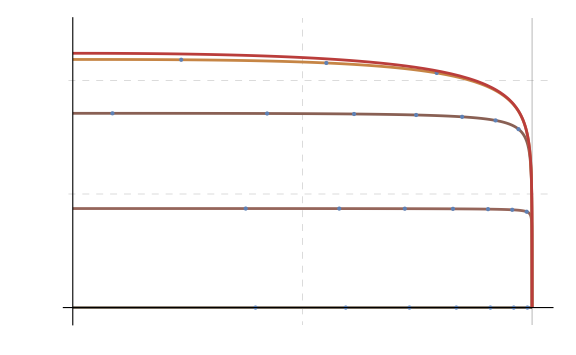

```mathematica
DisplayCartesianTPlots[Table[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,{},constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->eval,L[0]->0},0,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,L[λ]==0]][[1]],{eval,{0,0.01,0.1,1,10}}],{},True]
```

We can easily see that the ‘direct’ geodesic, corresponding to falling with no energy per unit mass e = 0 and hence having no displacement in the ∂_t  coordinate, is the one that survives the longest. Since travellers crossing from the outside of the event horizon must by definition have some non-zero e, we know engines can be useful to extend our life in practical circumstances.
Let’s see how this situation looks when we’re only taking into account angular momentum per unit mass l, with e = 0:

NDSolve::ndsz: At λ == 2.4736, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.13544, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 3.10834, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

7.53371

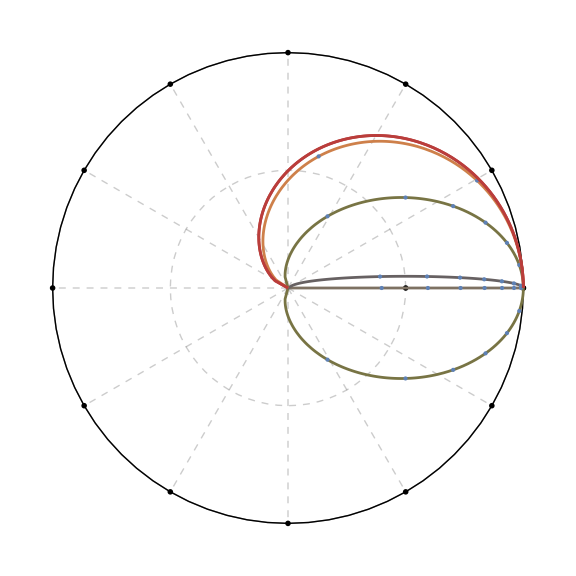

```mathematica
DisplayPolarPhiPlots[Table[solveEquations[eqOfMotion,u,a,unorm,{},constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->Lval},0,1,{0,π},And[γt'[λ]==γt''[λ]==0,aϕ[λ]==ar[λ]==at[λ]==0,e[λ]==0],γϕ][[2]],{Lval,{-1,0,0.1,1,5,100,10000}}]]
```

We can even plot multiple geodesics inside a cylinder, showing behavior in the situation with nonzero L and e:

```mathematica
Show[Table[solveEquations[eqOfMotion,u,a,unorm,{},constants,{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->eval,L[0]->Lval},0,1,{0,π},And[aϕ[λ]==ar[λ]==at[λ]==0],γϕ][[3]],{eval,{-0.1,0,1}},{Lval,{-1,0,0.1}}],Graphics3D[{Opacity[0.2],Cylinder[{{0,0,25},{0,0,-20}},2],Mesh->All}],PlotRange->{{-2.1,2.1},{-2.1,2.1},Full}, Boxed->True]
```

NDSolve::ndsz: At λ == 2.195, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.78368, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.75761, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

5.62524

-Graphics3D-

## Accelerated motion graphs

Let’s see how acceleration changes the outcome:

NDSolve::ndsz: At λ == 1.33032, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 1.62795, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 1.63445, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

12.0232

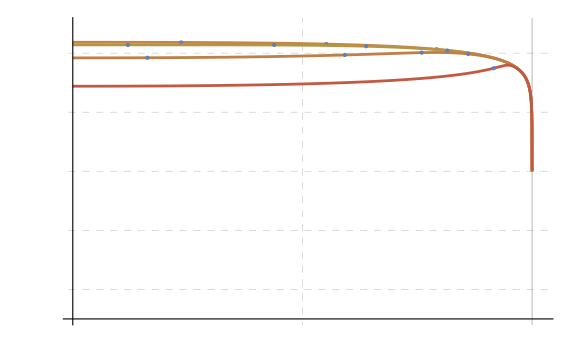

```mathematica
DisplayCartesianTPlots[Table[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify,constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->1,L[0]->0},aval,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==0,L[λ]==0],γt][[1]],{aval,{0,-0.65,-2.4,-10}}]]
```

This example for radial geodesics illustrates that we can ‘overshoot’ when we apply too much acceleration. Same situation for angular momentum:

NDSolve::ndsz: At λ == 1.20861, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.15443, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.08153, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

6.36531

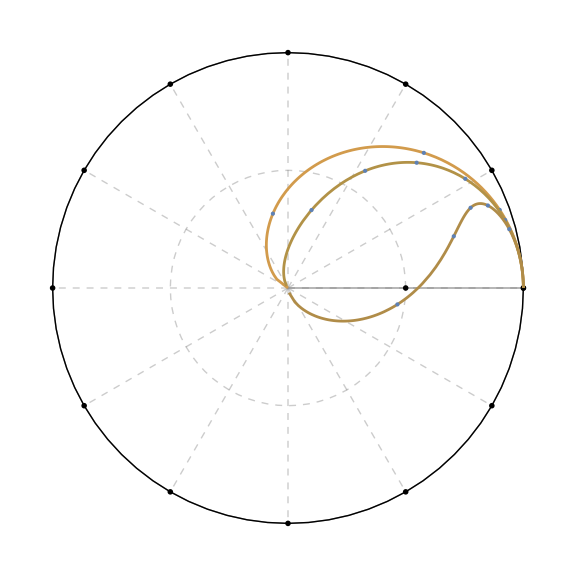

```mathematica
DisplayPolarPhiPlots[Table[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.5},aval,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[2]],{aval,{0,-0.65,-1.3}}]]
```

So, let’s stop accelerating the moment we kill our velocity and fall on the optimal geodesic:

NDSolve::ndsz: At λ == 1.33032, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1.35367} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.35281} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.35163} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::ndsz: At λ == 1.33032, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 1.62795, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

13.7222

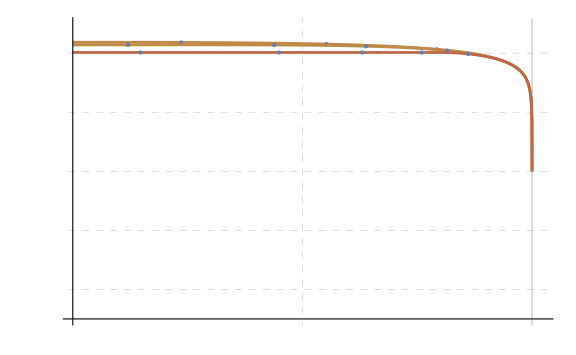

```mathematica
DisplayCartesianTPlots[Table[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.aϕ[λ]->0,{at[λ],ar[λ]}][[1]]//FullSimplify,constants[[2]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->1,L[0]->0},aval,1,{0,π},And[γϕ'[λ]==γϕ''[λ]==0,aϕ[λ]==0,L[λ]==0],γt][[1]],{aval,{0,-0.65,-2.4}}]]
```

NDSolve::ndsz: At λ == 1.20861, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.15443, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At λ == 2.08153, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

7.80652

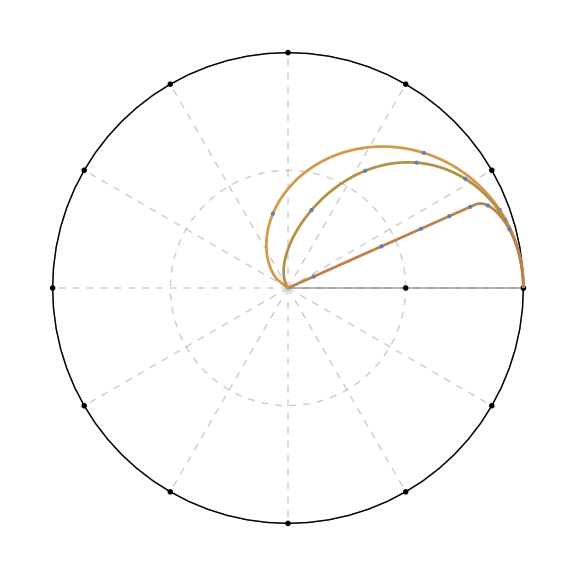

```mathematica
DisplayPolarPhiPlots[
Join[Table[solveEquations[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.5},aval,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[2]],{aval,{0,-0.65}}],
Table[solveEquationsUpToBestGeodesic[eqOfMotion,u,a,unorm,Solve[{a[α] a[-α]==amag^2,a[α] u[-α]==0}/.r[]->γr[λ]/.at[λ]->0,{aϕ[λ],ar[λ]}][[1]]//FullSimplify,constants[[1]],{γt[0]->0,γr[0]->1.99999M,γϕ[0]->0},{e[0]->0,L[0]->3.5},aval,1,{0,π},And[γt'[λ]==γt''[λ]==0,at[λ]==0,e[λ]==0],γϕ][[2]],{aval,{-1.3}}]]]
```

## Direct calculation of proper time depending on circumstances

Drawing orbits is a great starting point and a good visualisation, but we’re interested in some qualitative answers.
The proper time on a geodesic is described by the following integral:

```mathematica
IntegrateWithNoAccel[mass_,est_,Lst_]:=
NIntegrate[-1/(√(est^2-(1+(Lst^2 mass^2)/y^2)(1-(2mass)/y))),{y,2mass,0}]
```

What we need is expressions for e and L depending on r; it turns out these are possible to derive and in the case of purely radial infall, we have an analytic expression in terms of Carlson integrals:

```mathematica
ropt[M_,a_,e0_]:=If[a==0,-1,2M+e0/a]
CarlsonFromR[M_,a_,e0_,r_]:=CarlsonFromR[M,a,e0,r]=Module[{z1,z2,z3,ρ},
{z1,z2,z3}=-Flatten@Values@List@ToRules@Roots[( z^3+( -(- a e0 - 2 a^2 M))z^2+(a e0 -1/(2M)+e0^2/(2M)) z^2+(-a e0/M - 2 a^2 ) z+1/(2M)a^2)==0,z]+1/r;
ρ=1/r;
2/3 CarlsonRJ[z1,z2,z3,ρ]/Sqrt[2M]]
Carlson[M_,a_,e0_]:=CarlsonFromR[M,a,e0,2M]
CarlsonOptimal[M_,a_,e0_]:=(*CarlsonOptimal[M,a,e0]=*)Module[{rbang},
If[a==0,
Carlson[M,0,e0],
rbang=ropt[M,a,e0];
If[2M>=rbang>0,
Carlson[M,a,e0]-CarlsonFromR[M,a,e0,rbang]+CarlsonFromR[M,0,0,rbang],
Carlson[M,a,e0]
]
]
]
```

In the case of infall with e = 0, we do nat have an analytic expression but can nevertheless obtain a simple quadrature

```mathematica
rLopt[M_,a_,L0_]:=If[a==0,z==-1,Reduce[L0-a(-1/2 √(-1+(2 M)/z) z (3 M+z)-3 M^2 ArcTan[√(-1+(2 M)/z)])==0,{z},Reals]]
NτLR[M_,a_,L0_,r_]:=NIntegrate[-(1/(√(-(1+1/z^2(L0-a(-1/2 √(-1+(2 M)/z) z (3 M+z)-3 M^2 ArcTan[√(-1+(2 M)/z)]))^2)(1-(2M)/z)))),{z,r,0}]
NτL[M_,a_,L0_]:=NτLR[M,a,L0,2M]
NτLOptimal[M_,a_,L0_]:=(*NτLOptimal[M,a,L0]=*)Module[{rbang},
rbang=rLopt[M,a,L0];
If[Not[BooleanQ[rbang]] && 2M>=rbang[[2]]>=0,
NτL[M,a,L0]-NτLR[M,a,L0,rbang[[2]]]+NτLR[M,0,0,rbang[[2]]],
NτL[M,a,L0]
]
]
```

In the general case, we have to use an explicit quadrature and adjust at every step; the optimal way to thrust turns out to be always opposite to the 3-velocity in the frame of an optimally falling observer with e = L = 0.

```mathematica
de[r_,a_]:=Module[{},-a]
dL[r_,a_,M_]:=Module[{},-(r a)/(√((2M)/r-1))]
Quadrature[e0_,L0_,M_,a_,cuts_:10000]:=Module[{
sum=0,
dr=(1.9999M)/cuts,
rcur ,
Lcur =L0*M,
ecur=e0,
angle,
at,aphi,
γ },
γ= √(L^2/r^2+1+e^2((2M)/r-1)^-1);
rcur=1.99995M;
While[rcur>0.00005,
sum=sum+N[dr/(γ √((2M)/r-1))/.{L->Lcur,e->ecur,r->rcur}];
angle=If[Lcur==0,π/2,ArcTan[(rcur ecur)/(Lcur √((2M)/rcur-1))]];
at = - Sin[angle]*a;
aphi = - Cos[angle]*a;
ecur=If[ecur>0,ecur+de[rcur,at]*dr,0];
Lcur=If[Lcur>0,Lcur+dL[rcur,aphi,M]*dr,0];
rcur=rcur-dr;
];
sum]
```

## Radial infall gains

Using these, we can draw some graphs:

```mathematica
dataCarlsonOptimal=Flatten[Table[{a,e0,CarlsonOptimal[1,a,e0]//N//Re},{a,-5,0,0.05},{e0,0,5,0.05}],1];
dataCarlsonGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[1,#[[2]],0]})&/@dataCarlsonOptimal;
```

3.75435

22.201

1.74949

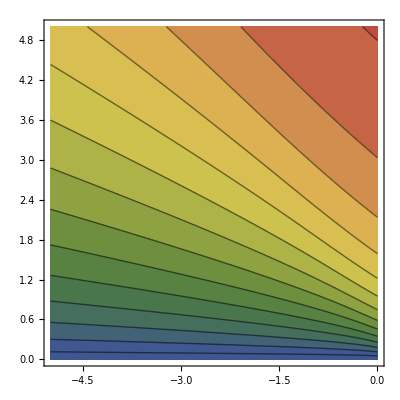

```mathematica
ListContourPlot[dataCarlsonOptimal,ColorFunction->(ColorData["DarkRainbow"][1-#/π]&),ColorFunctionScaling->False,Contours->Range[π,0,-π/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","e_0"},PlotRange->All,FrameStyle->Black]
```

We also want to see the graphs for the gain function:

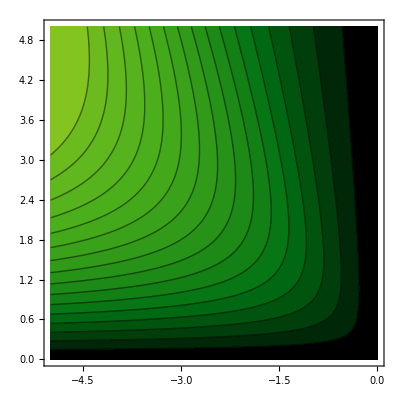

```mathematica
ListContourPlot[dataCarlsonGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","e_0"},PlotRange->All,FrameStyle->Black]
```

## Infall with e = 0 gains

```mathematica
dataNLOptimal=Flatten[Table[{a,L0,NτLOptimal[1,a,L0]//N//Re},{a,-5,0,0.5/10},{L0,0,5,0.5/10}],1];
dataNLGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[1,0,#[[2]]]})&/@dataNLOptimal;
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

1705.79

29.742

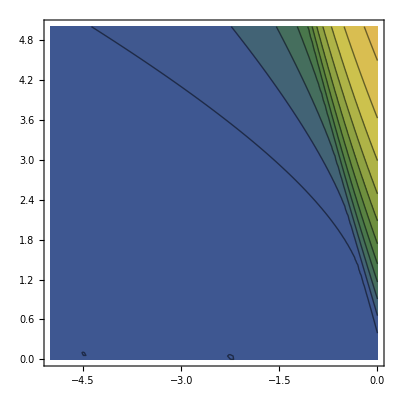

```mathematica
ListContourPlot[dataNLOptimal,ColorFunction->(ColorData["DarkRainbow"][1-#/π]&),ColorFunctionScaling->False,Contours->Range[π,0,-π/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],LabelStyle->texStyle,BaseStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","L_0 [M]"},PlotRange->All,FrameStyle->Black]
```

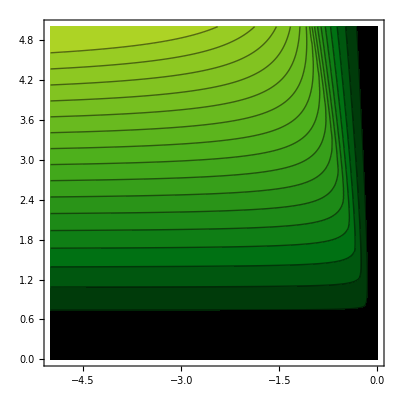

```mathematica
ListContourPlot[dataNLGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"\\alpha [m^{-1}]","L_0 [M]"},PlotRange->All,FrameStyle->Black]
```

## General case gains

```mathematica
genPlotsGeneralCase[a_,M_:1,ticks_:100,quads_:10000]:=Module[{
generalPlotData,
generalGain
},
generalPlotData=Flatten[Table[{L0,e0,Quadrature[e0,L0,M,a,quads]},{L0,0,5,5/ticks},{e0,0,5,5/ticks}],1];
generalGain=({#[[1]],#[[2]],#[[3]]/IntegrateWithNoAccel[M,#[[2]],#[[1]]]})&/@generalPlotData;
Return[
{ListPlot3D[generalPlotData,PlotRange->All,ColorFunction->Function[{x,y,par},ColorData["DarkRainbow"][1-par/(M π)]],ColorFunctionScaling->False,AxesLabel->MaTeX/@{"L_0 [M]","e_0","\\tau [m]"},BaseStyle->texStyle,LabelStyle->texStyle,AxesStyle->Black,BoxStyle->Black],
ListContourPlot[generalPlotData,ColorFunction->(ColorData["DarkRainbow"][1-#/(π M)]&),ColorFunctionScaling->False,Contours->Range[π M,0,-π M/16],PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\tau [m]"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"L_0 [M]","e_0"},PlotRange->All,FrameStyle->Black],
ListPlot3D[generalGain,ColorFunction->Function[{x,y,par},ColorData["AvocadoColors"][Log[5,par]]],ColorFunctionScaling->False,AxesLabel->MaTeX/@{"L_0 [M]","e_0","\\tau [m]"},BaseStyle->texStyle,LabelStyle->texStyle,AxesStyle->Black,BoxStyle->Black,PlotRange->All],
ListContourPlot[generalGain,Contours->16,ColorFunction->(ColorData["AvocadoColors"][Log[5,#]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[Automatic,LegendLabel->MaTeX@"\\frac{\\tau}{\\tau_{\\alpha=0}}"],BaseStyle->texStyle,LabelStyle->texStyle,FrameLabel->MaTeX/@{"L_0 [M]","e_0"},PlotRange->All,FrameStyle->Black]
}
]
]
```

```mathematica
Table[genPlotsGeneralCase[a],{a,-0.5,-3,-0.5}]
```

$Aborted

## Gains for some measured black holes

Finally, we could ask ourselves: how much can we really gain? For this purpose, we will use some realistic values for acceleration (on the order of g to 1000g; see paper for longer discussion), and the black hole masses for Sagittarius A*, Messier 87*, and Phoenix A* (the largest black hole found in nature).

```mathematica
g=10/((3*10^8)^2)
```

1/9000000000000000

```mathematica
sol=1500
```

1500

For radial infall:

```mathematica
ColumnForm[Flatten[Table[{M,a,e,CarlsonOptimal[M,a,e]//N//Re,CarlsonOptimal[M,a,e]/(3*10^8)//N//Re,CarlsonOptimal[M,a,e]/(3*10^8*60*60)//N//Re,(CarlsonOptimal[M,a,e]//N//Re)/(CarlsonOptimal[M,0,e]//N//Re)-1},{M,{4.297*10^6*sol,6.5*10^9*sol,10^11 sol}},{a,{0,-g,-10g,-100g,-1000g}},{e,{1,10}}],1]]
```

{{6.4455×10^9,0,1,8.594×10^9,28.6467,0.00795741,0.},{6.4455×10^9,0,10,1.26295×10^9,4.20983,0.0011694,0.}}
{{6.4455×10^9,-1/9000000000000000,1,8.594×10^9,28.6467,0.00795741,2.45543×10^-7},{6.4455×10^9,-1/9000000000000000,10,1.26055×10^9,4.20184,0.00116718,-0.00189891}}
{{6.4455×10^9,-1/900000000000000,1,8.59402×10^9,28.6467,0.00795743,2.45543×10^-6},{6.4455×10^9,-1/900000000000000,10,1.26294×10^9,4.20978,0.00116938,-0.0000113972}}
{{6.4455×10^9,-1/90000000000000,1,8.59421×10^9,28.6474,0.0079576,0.0000245546},{6.4455×10^9,-1/90000000000000,10,1.26296×10^9,4.20986,0.0011694,5.76047×10^-6}}
{{6.4455×10^9,-1/9000000000000,1,8.59611×10^9,28.6537,0.00795936,0.000245571},{6.4455×10^9,-1/9000000000000,10,1.26303×10^9,4.21011,0.00116948,0.0000666028}}
{{9.75×10^12,0,1,1.3×10^13,43333.3,12.037,0.},{9.75×10^12,0,10,1.91044×10^12,6368.14,1.76893,-1.11022×10^-16}}
{{9.75×10^12,-1/9000000000000000,1,1.30048×10^13,43349.4,12.0415,0.000371494},{9.75×10^12,-1/9000000000000000,10,1.91064×10^12,6368.78,1.76911,0.000100768}}
{{9.75×10^12,-1/900000000000000,1,1.30484×10^13,43494.6,12.0818,0.00372073},{9.75×10^12,-1/900000000000000,10,1.91237×10^12,6374.57,1.77071,0.00100875}}
{{9.75×10^12,-1/90000000000000,1,1.34905×10^13,44968.4,12.4912,0.0377328},{9.75×10^12,-1/90000000000000,10,1.92994×10^12,6433.12,1.78698,0.0102042}}
{{9.75×10^12,-1/9000000000000,1,1.74299×10^13,58099.7,16.1388,0.340762},{9.75×10^12,-1/9000000000000,10,2.13109×10^12,7103.64,1.97323,0.115496}}
{{150000000000000,0,1,2.×10^14,666667.,185.185,0.},{150000000000000,0,10,2.93914×10^13,97971.4,27.2143,0.}}
{{150000000000000,-1/9000000000000000,1,2.01146×10^14,670486.,186.246,0.00572948},{150000000000000,-1/9000000000000000,10,2.94371×10^13,98123.6,27.2565,0.00155299}}
{{150000000000000,-1/900000000000000,1,2.1169×10^14,705633.,196.009,0.0584496},{150000000000000,-1/900000000000000,10,2.98561×10^13,99520.2,27.6445,0.0158082}}
{{150000000000000,-1/90000000000000,1,2.89604×10^14,965345.,268.151,0.448018},{150000000000000,-1/90000000000000,10,3.50659×10^13,116886.,32.4684,0.193065}}
{{150000000000000,-1/9000000000000,1,3.90493×10^14,1.30164×10^6,361.567,0.952463},{150000000000000,-1/9000000000000,10,1.91031×10^14,636771.,176.881,5.49956}}

We see that we can get some significant gains. Let’s also pick parameters corresponding to a ‘realistic’ infall, e = 0.8 and L = √12M

```mathematica
ColumnForm[Flatten[Table[{M,a,Quadrature[0.8,Sqrt[12],M,a,10000]//N//Re,Quadrature[0.8,Sqrt[12],M,a,10000]/(3*10^8)//N//Re,Quadrature[0.8,Sqrt[12],M,a,10000]/(3*10^8*60*60)//N//Re,(Quadrature[0.8,Sqrt[12],M,a,10000]//N//Re)/(Quadrature[0.8,Sqrt[12],M,0,10000]//N//Re)-1},{M,{4.297*10^6*sol,6.5*10^9*sol,10^11 sol}},{a,{0,-g,-10g,-100g,-1000g}}],1]]
```

28.8827

{6.4455×10^9,0,4.84664×10^9,16.1555,0.00448763,0.}
{6.4455×10^9,-1/9000000000000000,4.84664×10^9,16.1555,0.00448763,2.56068×10^-7}
{6.4455×10^9,-1/900000000000000,4.84665×10^9,16.1555,0.00448764,2.56068×10^-6}
{6.4455×10^9,-1/90000000000000,4.84676×10^9,16.1559,0.00448774,0.0000256076}
{6.4455×10^9,-1/9000000000000,4.84788×10^9,16.1596,0.00448878,0.000256153}
{9.75×10^12,0,7.33143×10^12,24438.1,6.78836,0.}
{9.75×10^12,-1/9000000000000000,7.33427×10^12,24447.6,6.79099,0.000387544}
{9.75×10^12,-1/900000000000000,7.35997×10^12,24533.2,6.81479,0.00389309}
{9.75×10^12,-1/90000000000000,7.63054×10^12,25435.1,7.06532,0.0407985}
{9.75×10^12,-1/9000000000000,1.35402×10^13,45134.,12.5372,0.846872}
{150000000000000,0,1.12791×10^14,375971.,104.436,0.}
{150000000000000,-1/9000000000000000,1.13469×10^14,378229.,105.064,0.00600574}
{150000000000000,-1/900000000000000,1.20082×10^14,400272.,111.187,0.0646374}
{150000000000000,-1/90000000000000,2.85341×10^14,951137.,264.205,1.52982}
{150000000000000,-1/9000000000000,3.99353×10^14,1.33118×10^6,369.771,2.54064}

In the most extreme case, we more than triple our survival time!

For more information and the math behind all this, check out the paper on arXiv.